#### Exact

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
rp=√(x^2+y^2+(z-z0 Sin[ω t])^2)
```

√(x^2+y^2+(z-z0 Sin[t ω])^2)

```mathematica
rm=√(x^2+y^2+(z+z0 Sin[ω t])^2)
```

√(x^2+y^2+(z+z0 Sin[t ω])^2)

```mathematica
φ=e/rp-e/rm
```

e/(√(x^2+y^2+(z-z0 Sin[t ω])^2))-e/(√(x^2+y^2+(z+z0 Sin[t ω])^2))

```mathematica
Ax=0
```

0

```mathematica
Ay=0
```

0

```mathematica
Az=(e/c) z0 ω Cos[ω t](1/rp+1/rm)
```

(e z0 ω Cos[t ω] (1/(√(x^2+y^2+(z-z0 Sin[t ω])^2))+1/(√(x^2+y^2+(z+z0 Sin[t ω])^2))))/c

```mathematica
Ex= ReplaceAll[D[φ,x]-1/c D[Ax,t],{y->0,z->0}]
```

0

```mathematica
Ey=ReplaceAll[D[φ,y]-1/c D[Ay,t],y->0]
```

0

```mathematica
Ez=Simplify[ReplaceAll[D[φ,z]-1/c D[Az,t],{y->0,z->0}]]
```

(2 e z0 (c^2+(x^2+z0^2) ω^2) Sin[t ω])/(c^2 (x^2+z0^2 Sin[t ω]^2)^(3/2))

```mathematica
Hx=ReplaceAll[D[Az,y]-D[Ay,z],y->0]
```

0

```mathematica
Hy=ReplaceAll[D[Ax,z]-D[Az,x],{y->0,z->0}]
```

(2 e x z0 ω Cos[t ω])/(c (x^2+z0^2 Sin[t ω]^2)^(3/2))

```mathematica
Hz=D[Ay,x]-D[Ax,y]
```

0

```mathematica
Solve[t0==t-√(x^2+y^2+(z-z0 Sin[ω t0])^2),t0]
```

Solve[t0==t-√(x^2+y^2+(z-z0 Sin[t0 ω])^2),t0]

```mathematica
Solve[t0^2==x^2+y^2,t0]
```

{{t0→-√(x^2+y^2)},{t0→√(x^2+y^2)}}

#### Dipole

1.25664

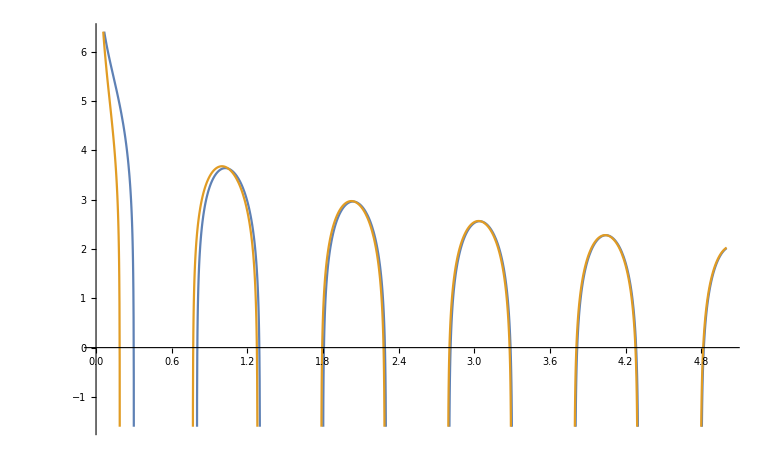

```mathematica
f=0.4π
Plot[{Log[4π^2Sin[2π x+f]/x],Log[4π^2Sin[2π x+f]/x+2π Cos[2π x+f]/x^2]},{x,0.01,5}]
```

1.56765

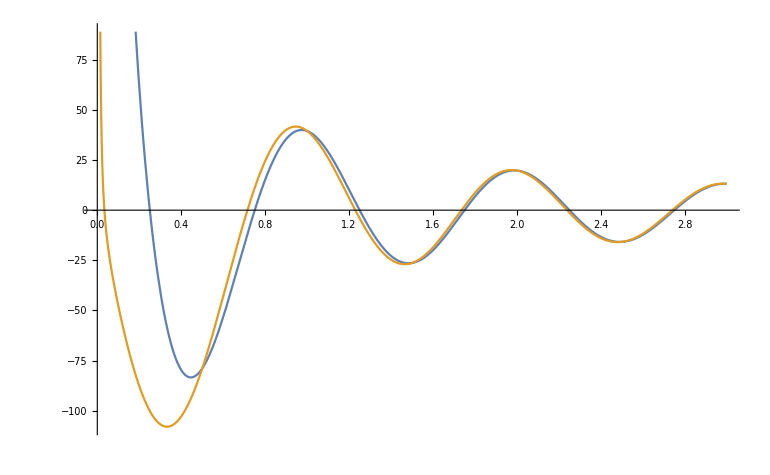

```mathematica
f=0.499π
Plot[{4π^2Sin[2π x+f]/x,4π^2Sin[2π x+f]/x+2π Cos[2π x+f]/x^2},{x,0,3}]
```

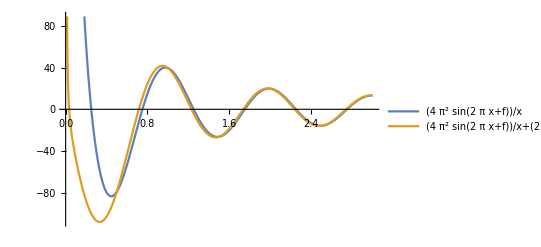

```mathematica
Plot[{(4 π^2 Sin[2 π x+f])/x,(4 π^2 Sin[2 π x+f])/x+(2 π Cos[2 π x+f])/x^2},{x,0,3},PlotLegends->"Expressions"]
```

```mathematica
Ez=e z0 w^2/c^2 Sin[w t-w/c x]/x
Hy=e z0 w^2/c^2 Sin[w t-w/c x]/x+e z0 w/c Cos[w t-w/c x]/x^2
```

(e w^2 z0 Sin[t w-(w x)/c])/(c^2 x)

(e w z0 Cos[t w-(w x)/c])/(c x^2)+(e w^2 z0 Sin[t w-(w x)/c])/(c^2 x)

```mathematica
D[Ez,x]
```

-(e w^3 z0 Cos[t w-(w x)/c])/(c^3 x)-(e w^2 z0 Sin[t w-(w x)/c])/(c^2 x^2)

```mathematica
D[Hy,t]
```

(e w^3 z0 Cos[t w-(w x)/c])/(c^2 x)-(e w^2 z0 Sin[t w-(w x)/c])/(c x^2)

```mathematica
Simplify[D[Ez,x]+D[Hy,t]/c]
```

-(2 e w^2 z0 Sin[w (t-x/c)])/(c^2 x^2)

```mathematica
D[Ez,t]
```

(e w^3 z0 Cos[t w-(w x)/c])/(c^2 x)

```mathematica
D[Hy,x]
```

-(2 e w z0 Cos[t w-(w x)/c])/(c x^3)-(e w^3 z0 Cos[t w-(w x)/c])/(c^3 x)

```mathematica
Simplify[D[Hy,x]-D[Ez,t]/c]
```

-(2 e w (c^2+w^2 x^2) z0 Cos[w (t-x/c)])/(c^3 x^3)